# .7fLinear Regression by Folding

Brian Beckman
18 Feb 2018

## Introduction

Linear systems appear everywhere, and, where they don’t appear naturally, linear approximations abound because non-linear systems are often intractable. Examples comprise machine learning, control, dynamics, robotics, and many more.

Linear regression is the standard technique for estimating the parameters or coefficients of a linear system. Usually, authors sweep linear regression under the rug, presumably because readers know all about effective ways to perform it. However, I have found this presumption not to be true. Time and again, I see code that employs the normal equations directly (that's inefficient and exposed to over-fitting), computes matrix inverses (that's risky), or abuses neural nets (a sledgehammer) to open a walnut (linear regression). 

This paper shows efficient, reliable methods for very general linear regression: recurrent least squares and Kalman folding. These are amongst the best known methods for linear regression. These methods automatically regularize their.7f fits based on input a-priori estimates and covariances. We relate this automatic regularization to .7fBayesian maximum posterior or MAP curve-fitting.

## Motivating Example

Find best-fit, unknowns m, b, where z≈m x+b, given known data (z_1,z_2,…,z_k) and (x_1,x_2,…,x_k). Write this system as a matrix equation and remember the symbols Ζ (observations, known), A (partials, known), and Ξ (model, state, unknown parameters to be estimated). Rows of Ζ and A come in matched pairs.

Ζ_(k×1)  =  (z_1
z_2
⋮
z_k)  =  (x_1 | 1
x_2 | 1
⋮ | ⋮
x_k | 1)·(m
b) + noise  =  A_(k×2)·Ξ_(2×1)+samples of NormalDistribution[0,σ_Ζ]

This extends to any linear system with any number of parameters.7f (we have two) and with tensors in the matrix slots.

Ground Truth

Test the method as follows: make some data by sampling a line specified by ground truth m and b, then adding some noise. Run the faked data through our estimation procedures and see how close the estimates come to the ground truth. In the real world, we don’t know ground truth, so it’s paramount that we trust the method before deploying it. Build up trust by testing.

```mathematica
ClearAll[groundTruth,m,b];
groundTruth={m,b}={0.5,-1./3.};
```

Partials

The partials A are a (column) vector of co-vectors (row vectors). Each co-vector is the gradient of the observation model, namely of A·Ξ, with respect to Ξ, evaluated at a specific Ξ. Gradients are co-vectors, that is, linear transformations of vectors. This fact drives  the dual problem, below.

```mathematica
ClearAll[nData,min,max];
nData=119;min=-1.;max=3.;
ClearAll[partials];
partials=Array[{#,1.0}&,nData,{min,max}];
Short[partials,3]
```

{{-1.,1.},{-0.966102,1.},«115»,{2.9661,1.},{3.,1.}}

Fake Data

```mathematica
ClearAll[fake];
fake[n_,σ_,A_,{m_,b_}]:=
Table[
RandomVariate[NormalDistribution[0,σ]]+A⟦i⟧.{m,b},
{i,n}];
```

```mathematica
ClearAll[data,noiseSigma];
noiseSigma=0.65;
data=fake[nData,noiseSigma,partials,groundTruth];
Short[data,3]
```

{-1.13515,-0.804982,-1.20757,«114»,0.546946,1.1458}

Model

Try the Wolfram built-in. The estimated m and b are reasonably close to the ground truth.

```mathematica
ClearAll[model];
model=LinearModelFit[{partials⟦All,1⟧,data}ᵀ,ξ,ξ];
Normal[model]
```

-0.213082+0.441843 ξ

Un-comment the following line to see everything Wolfram has to say about this model (it’s a lot of data).

```mathematica
(*Association[(#->model[#])&/@model["Properties"]]*)
```

The plot shows that Wolfram does an acceptable job of estimating the parameters m and b that define the line:

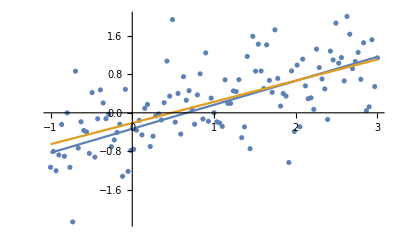

```mathematica
Show[ListPlot[{partials⟦All,1⟧,data}ᵀ],
Plot[{m ξ+b,model[ξ]},{ξ,min,max}]]
```

In the following, we show several methods that are all mathematically equivalent, but have different operational characteristics regarding memory usage, numerical risk, and over-fitting.

Normal Equations

Equation 1 can be solved for a value of Ξ that minimizes the square error J(Ξ)=^def(Ζ-A·Ξ)ᵀ·(Ζ-A·Ξ). Because the noise 𝒩(0,σ) has zero mean (or zero bias), The solution turns out to be exactly what one would get from naive algebra.  Aᵀ·A is square. When it is invertible,

(Aᵀ·A)^-1·Aᵀ·Z  =  Ξ

That gives the same answer as Wolfram’s built-in:

```mathematica
Inverse[partialsᵀ.partials].partialsᵀ.data
```

{0.441843,-0.213082}

The matrix (Aᵀ·A)^-1·Aᵀ is the Moore-Penrose left pseudoinverse. Wolfram has a built-in for it:

```mathematica
PseudoInverse[partials].data
```

{0.441843,-0.213082}

(Aᵀ·A)^-1·Aᵀ·Ζ is a nasty computation at even moderate scale: in memory usage, in time, and in numerical risk. Eliminate these defects with a recurrence.

## Recurrence

Fold the following recurrence over Ζ and A:

ψ←(Λ+aᵀ·a)^-1·(aᵀ·ζ+Λ·ψ)
Λ←(Λ+aᵀ·a)

where ψ is the current estimate of Ξ, a and ζ are matched rows of A and Ζ, and Λ accumulates Aᵀ·A.

Derive the recurrence as follows: Treat the estimate-so-far,

ψ_(so-far)=^def(Aᵀ·A)^-1·Aᵀ·Ζ_(so-far)

as just one more observation with information matrix (proportional to inverse covariance) Λ=A_(so-far)ᵀ·A_(so-far). The scalar performance or squared error of the estimate, so far, is

J(x)  =  (Ζ_(so-far)-A_(so-far)·x)ᵀ·(Ζ_(so-far)-A_(so-far)·x)  =  (x-ψ_(so-far))ᵀ·Λ·(x-ψ_(so-far))

where x is the unknown true parameter vector, z_(so-far) is the column vector of all observations so-far, and Λ=A_(so-far)ᵀ·A_(so-far) . Adding a new observation, ζ and its corresponding partial row co-vector a, increases the error J(x) by (ζ-a·x)ᵀ·(ζ-a·x). Minimize the new total error with respect to x to find the recurrence (exercise).

Bootstrap the recurrence with initial values of ψ and Λ, namely ψ_0 and Λ_0. We show below that choices for the values of these strongly affect regularization against over-fitting.

The example below starts with ψ_0=(0 | 0)ᵀ and Λ_0=((10^-6 | 0)(0 | 10^-6)).

```mathematica
ClearAll[update];
update[{ψ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{Inverse[Π].(aᵀ.ζ+ Λ.ψ),Π}];
MatrixForm/@
({({{mBar}, {bBar}}),Π}=Fold[update,
{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.441843
-0.213082),(280.356 | 119.
119. | 119.)}

The estimates mBar and bBar are exactly what we got from Wolfram’s built-in. For this example, the choice of ψ_0 and Λ_0 had negligible effect.

The mappings of List over the data and partials convert them into column vectors, as required by the recurrences in linear-algebra form (column vectors and row co-vectors). The earlier applications of Wolfram built-ins and the normal equations are promiscuous: they treat lists as column vectors or row-vectors as needed by implicit context and compute inner (dot) products as if the distinction did not matter. Python’s numpy has the same dubious feature. I call it dubious because such looseness inhibits extension to higher dimensions and .7ftensors. If we are scrupulous in expressing column vectors as matrices with one column and co-vectors as matrices with one row, we have an easier time with extensions. Now that we know, we just pay attention.

We might also fold this recurrence over an asynchronous stream, in which case it runs in constant memory, O(n), where n is the dimension (length) of Ξ, same as the dimension of each row of A.

The final value of Λ (called Π in the code, a returned value), is A_full ᵀ·A_full+Λ_0. The difference between Π and A_full ᵀ·A_full must be Λ_0:

```mathematica
Π-partialsᵀ.partials
```

{{1.×10^-6,0.},{0.,1.×10^-6}}

The covariance of the estimate Ξ is ((n-1)/(n-2))*Variance [ Ζ-A·Ξ ]*Λ^-1 except for a small contribution from the a-priori information Λ_0. The correction factor ((n-1)/(n-2)) is a generalization .7fof Bessel’s correction. The 2 in (n-2) in the denominator is due to the fact that we’re estimating two parameters from the data (see VAN DE GEER, Least Squares Estimation, Volume 2, pp. 1041–1045, in Encyclopedia of Statistics in Behavioral Science, Eds. Brian S. Everitt & David C. Howell, Wiley, 2005). The denominator of the correction, in general, is n-p, where n is the number of data and p is the number of parameters being estimated.

```mathematica
Inverse[partialsᵀ.partials]*(nData-1)/(nData-2)*Variance[data-partials.{mBar,bBar}]//MatrixForm
```

(0.00234302 | -0.00234302
-0.00234302 | 0.00552)

Except for the reversed order, this is the same covariance matrix that Wolfram reports:

```mathematica
Reverse@(Reverse/@model["CovarianceMatrix"])//MatrixForm
```

(0.00234302 | -0.00234302
-0.00234302 | 0.00552)

Don’t Invert That Matrix.7f

See https://www.johndcook.com/blog/2010/01/19/dont-invert-that-matrix/ 

In general, when you see a matrix expression A^-1·B, you usually can and should replace it with linsolve(A,B).

Replace Inverse with LinearSolve:

```mathematica
ClearAll[update];
update[{ψ_,Λ_},{ζ_,a_}]:=
With[{Π=(Λ+aᵀ.a)},
{LinearSolve[Π,(aᵀ.ζ+Λ.ψ)],Π}];
MatrixForm/@({({{mBar}, {bBar}}),Π}=Fold[update,
{({{0}, {0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@data,List/@partials}ᵀ])
```

{(0.441843
-0.213082),(280.356 | 119.
119. | 119.)}

exactly as above.

We have eliminated memory bloat by accumulating estimate updates one observation at a time, each with its paired partial. We reduce computation time and numerical risk by solving a linear system instead of inverting a matrix.

## The Dual Problem

When the model --- the thing we’re trying to estimate --- is a co-vector (row-vector), e.g., a gradient, we have the dual (transposed) problem. In that case, the observations Ω and the model Γ are now.7f co-vectors with elements ω and γ  instead of ζ and ψ. The co-partials Θ (replacing A) are now a co-vector of column vectors θ. The observation equation looks like Ω=Γ·Θ and the error-so-far like (x-γ)·Λ·(x-γ)ᵀ, where Λ=Θ_(so-far)·Θ_(so-far)ᵀ. We don’t change the name of Λ because it’s symmetric. Adding a new observation ω introduces new error (ω-x·θ)·(ω-x·θ)ᵀ. Minimizing the total error yields

γ←(γ·Λ+ω·θ ᵀ ).(Λ+θ·θ ᵀ )^-1
Λ←(Λ+θ·θ ᵀ )

straight transposes of equation 3. LinearSolve operates on the transposed right-hand side of the recurrence, and we transpose the solution to get the recurrence. We apply this dual model to the transpose of the original data:

```mathematica
Short[Transpose/@List/@partials,3]
```

{{{-1.},{1.}},{{-0.966102},{1.}},«115»,{{2.9661},{1.}},{{3.},{1.}}}

```mathematica
ClearAll[coUpdate];
coUpdate[{γ_,Λ_},{ω_,θ_}]:=
With[{Π=(Λ+θ.θᵀ)},
{LinearSolve[Π,Λ.γᵀ+θ.ωᵀ]ᵀ,Π}];
MatrixForm/@Fold[coUpdate,
{({{0, 0}}),({{1.0*^-6, 0}, {0, 1.0*^-6}})},
{List/@List/@data,Transpose/@List/@partials}ᵀ]
```

{(0.441843 | -0.213082),(280.356 | 119.
119. | 119.)}

Application of the Dual Problem

The finite-difference method of policy-gradient machine learning provides a motivating example of the dual problem (see http://www.scholarpedia.org/article/Policy_gradient_methods). 

Imagine a scalar function J(θ) of a column K-vector θ_(K×1). We want to estimate its gradient co-vector ∇J, given a batch of ℐ random increments ΔΘ_(K×ℐ), from the system ∇J·ΔΘ=Δ J. Here, ∇J takes the role of the model whose state parameters Γ we want to estimate, ΔΘ takes the role of the partials of the model w.r.t. those parameters, and Δ J takes the role of measured data. Let Δ J_(ℐ×1) be a batch of observed increments to J and ΔΘ_(K×ℐ) be a matrix of the ℐ corresponding column-vector random increments to the input vectors θ_(K×1). The right pseudoinverse RPI=^def(ΔΘ_(K×ℐ)·ΔΘ_(K×ℐ)^ᵀ)^-1·ΔΘ_(K×ℐ)^ᵀ solves ∇ J_(ℐ×1)·ΔΘ_(K×ℐ)=Δ J_(ℐ×1) to yield ∇ J_(ℐ×1)≈Δ J_(ℐ×1)·RPI. 

Use the co-update recurrence for this problem.

## Regularization By A-Priori: Example

Chris Bishop’s book Pattern Recognition and Machine Learning has an extended example fitting polynomials, linear in their coefficients, starting in section 1.1. The higher the order of the polynomial, the more it tends to over-fit a small data set. The example progresses into maximum posterior or MAP regularization as a cure for over-fitting. 

Recursive least squares and the mathematically equivalent Kalman fold require an a-priori estimate of the coefficients and a-priori uncertainty of the coefficients as information matrix or covariance matrix, respectively. The Kalman filter additionally requires an estimate of observation noise. Both recurrent least-squares and the Kalman filter automatically regularize the fit, reducing over-fitting for even modest magnitudes of the uncertainty of the a-priori estimates.

First, a sequence of n inputs or features, equally spaced in [0..1]. Like MATLAB linspace.

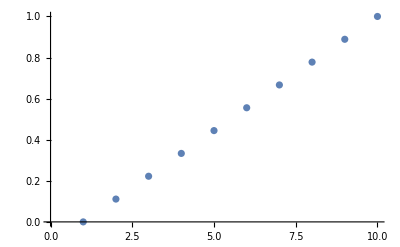

```mathematica
ClearAll[bishopTrainingSetX];
bishopTrainingSetX[n_]:=Array[Identity,n,{0.,1.}];
ListPlot[bishopTrainingSetX[10]]
```

Ground truth is a single cycle of a sine wave. Add some noise to a sample of the ground truth taken at the values of the training set X.

```mathematica
ClearAll[bishopFakeY,bishopGroundTruthY];
bishopGroundTruthY[xs_]:=Sin[2.π#]&/@xs;
bishopFakeY[xs_,σ_]:=
With[{n=Length@xs},
bishopGroundTruthY[xs]
+RandomVariate[NormalDistribution[0.,σ],n]];
```

Bishop doesn’t state his a-priori uncertainties, so I guess σ_(z=t)=0.30 to create the fake data set. We get back to Bishop’s α and β from figure 1.17 (page 32), which imply some uncertainties when we analyze Bishop’s equations 1.70 through 1.72 for Bayesian maximum-posterior (MAP), in the light of Kalman filtering.

Take a sample and assign it the name bishopTrainingSet. It isn’t his actual training set (which I didn’t find in print), just my simulation of it.

```mathematica
ClearAll[bishopTrainingSet,bishopFake,bishopFakeSigma];
bishopFake[n_,σ_]:=
With[{xs=bishopTrainingSetX[n]},
With[{ys=bishopFakeY[xs,σ]},
{xs,ys}]];
bishopFakeSigma=0.30;
bishopTrainingSet=bishopFake[10,bishopFakeSigma];
```

Make a plot like Bishop’s figure 1.7 (page 10).

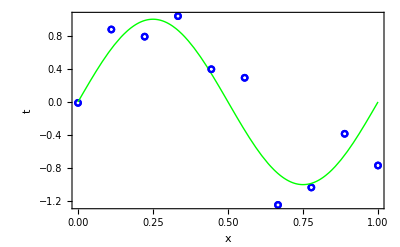

```mathematica
With[{lp=ListPlot[bishopTrainingSetᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set the scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
lp (* again to overdraw the plot *)},
Frame->True,
FrameLabel->{"x","t"}]]
```

Write a function to build up partials for both recurrent least squares and Kalman fold. We quietly map the indeterminate 0^0 to 1

```mathematica
ClearAll[partialsFn];
partialsFn[order_,xs_]:=
Transpose@Quiet@Table[#^(i-1)/.{Indeterminate->1},{i,order+1}]&@xs;
MatrixForm@partialsFn[6,{Subscript[x, 1],Subscript[x, 2],Subscript[x, Μ]}]
```

(1 | x_1 | x_1^2 | x_1^3 | x_1^4 | x_1^5 | x_1^6
1 | x_2 | x_2^2 | x_2^3 | x_2^4 | x_2^5 | x_2^6
1 | x_Μ | x_Μ^2 | x_Μ^3 | x_Μ^4 | x_Μ^5 | x_Μ^6)

The following mechanizes the normal equations; it’s unregularized and we expect it to over-fit.

```mathematica
ClearAll[normalPolyFit];
normalPolyFit[order_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
PseudoInverse[partialsFn[order,xs]].ys];
normalPolyFit[3,bishopTrainingSet]
```

{0.0102216,9.7893,-27.5611,17.2332}

The following recurrent least-squares is regularized by its a-priori estimate and a-priori information matrix.

```mathematica
ClearAll[polyFit];
polyFit[minInfo_][order_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{aPriori=List/@ConstantArray[0,order+1],
aPrioriInfo=minInfo*IdentityMatrix[order+1]},
Fold[update,{aPriori,aPrioriInfo},
{List/@ys,List/@partialsFn[order,xs]}ᵀ]]];
Manipulate[
polyFit[10^-logMinInfo][3,bishopTrainingSet]⟦1⟧,
{{logMinInfo,6},0,16,1,Appearance->"Open"}]
```

Bishop calls the following ϕ(x) in his equations 1.70 through 1.72 on page 31:

```mathematica
ClearAll[symbolicPowers];
symbolicPowers[variable_,order_]:=
partialsFn[order,{variable}]⟦1⟧;
symbolicPowers[Subscript[x, Α],6]
```

{1,x_Α,x_Α^2,x_Α^3,x_Α^4,x_Α^5,x_Α^6}

The foldable Kalman filter below sows out several versions of the covariance; we could reap and track them externally to monitor numerical issues, specifically, catastrophic cancelation in L and P. Such issues are routinely addressed by equivalent U D filtering, subject of another paper in this series.

```mathematica
ClearAll[kalmanUpdate,kalmanFit];
kalmanUpdate[Ζ_][{x_,P_},{z_,A_}]:=
Module[{D,KT,K,L},
D=Ζ+A.P.Aᵀ;
KT=LinearSolve[D,A.P];(* D and P are symmetric *)
K=KTᵀ(*P.Aᵀ.PseudoInverse[D]*);
L=IdentityMatrix[Length[P]]-K.A;
Sow[L.P,"P1"];
Sow[L.P.Lᵀ+K.Ζ.Kᵀ,"P2"];
Sow[P-K.D.Kᵀ,"P3"];
{x+K.(z-A.x),L.P}];
kalmanFit[σzSquared_,σxSquared_][order_,trainingSet_]:=
With[{xs=trainingSet⟦1⟧,ys=trainingSet⟦2⟧},
With[{aPrioriModel=List/@ConstantArray[0,order+1],
aPrioriCovariance=σxSquared*IdentityMatrix[order+1]},
Fold[kalmanUpdate[σzSquared*IdentityMatrix[1]],
{aPrioriModel,aPrioriCovariance},
{List/@ys,List/@partialsFn[order,xs]}ᵀ]]];
```

The following interactive demonstration shows all three methods, normalPolyFit, polyFit (recurrent least squares), and kalmanFit (Kalman folding) on Bishop’s training set.

When the information matrix in recurrent least squares is 10^-6, and when the a-priori covariance of the a-priori estimate in the Kalman filter is 10^6, both produce regularized estimates of the coefficients of high-order polynomial fits to the sine wave. In contrast, the normal equations over-fit the polynomial by interpolating (going through) every data point at order nine because a ninth-order polynomial fits our ten data points exactly: the normal equations are neither overdetermined nor underdetermined, but accidentally constitute an exactly solvable linear system.

Increasing logMinInfo decreases the magnitude of the a-priori information matrix in recurrent least squares. Increasing logSigmaXSquared increases the covariance (uncertainty) of the a-priori in the Kalman fold. Eventually, they over-fit the data completely, just like the normal equations. 

The computation of polyFit is wrapped in a Quiet form, which suppresses warnings about the initial Λ_0’s being ill-conditioned as its magnitude decreases. In real-world applications, such warnings would presage over-fitting and would be very useful. They’re suppressed here so as not to disrupt interactive exploration by the reader.

```mathematica
Manipulate[
Module[{x},
With[{terms=symbolicPowers[x,order]},
With[{polyFn={terms}.Quiet@polyFit[10^-logMinInfo]
[order,bishopTrainingSet]⟦1⟧,
nmPolyFn=terms.normalPolyFit[order,bishopTrainingSet],
kalmanFn={terms}.kalmanFit[bishopFakeSigma,10^logSigmaXSquared]
[order,bishopTrainingSet]⟦1⟧},
With[{lp=ListPlot[bishopTrainingSetᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
Plot[nmPolyFn,{x,0,1},PlotStyle->{Orange}],
Plot[kalmanFn,{x,0,1},PlotStyle->{Cyan}],
Plot[polyFn,{x,0,1},PlotStyle->{Purple}]},
Frame->True,
FrameLabel->{"x","t"}]]]]],
{{order,9},0,16,1,Appearance->{"Labeled","Open"}},
{{logMinInfo,6},0,16,1,Appearance->"Open"},
{{logSigmaXSquared,6},0,16,1,Appearance->"Open"}]
```

## Regularization and MAP

Bishop reports β=11.111… and α=0.005 in his figure 1.17 (page 32). These hyperparameters appear in his equations 1.70 through 1.72 (page 31), which look suspiciously like the equations for Kalman filtering. In particular, β purports to be 1/σ_w^2, implying that his a-priori uncertainty in the estimated parameters w is 0.30, suspiciously like the observation noise we guessed to create the fake training set. Paradoxically, α appears in equation 1.72 precisely where we would expect observation noise because Bishop’s matrix S looks just like D^-1 in our kalmanUpdate above. This observation noise is much to small to reproduce his figure 1.7 (page 10), so we have some work to do to confirm or refute our reconstructions.

Can we reproduce Bishop’s figure 1.17 (page 32) from his equations 1.70 through 1.72 (page 31)?

Can we get to Bishop’s figure 1.17 from his figure 1.7?

Can we reconcile (numerically) his maximum-posterior (MAP) treatment of equations 1.70 through 1.72 with our Kalman filter?

Reproducing Bishop’s MAP

Bishop’s equations 1.70 through 1.72 are reproduced here, noting that the dimensions of the identity matrix in the definition of S is Μ+1, where Μ is the order of the polynomial:

m(x)  =  β ϕ (x)ᵀ·S·∑_(n=1)^N ϕ (x_n)t_n

s^2(x)  =  β^-1+ϕ (x)ᵀ·S·ϕ (x)

S^-1  =^def  α I_(Μ+1)+β∑_(n=1)^N ϕ (x_n)·ϕ (x_n)ᵀ

First of all, ϕ (x_n) is a (Μ+1)-column vector of the powers of the n^th input (or feature) x_n, the dual of one row co-vector of our partials. Bishop calls the order of the polynomial Μ, and it’s mostly implicit in his treatment. 

We do not use the promiscuous form of column vector as a straight, one-level list lest we lose Bishop’s transposes; map List over the training data to convert them to proper column vectors, as above. As above, quietly map the indeterminate 0^0 to 1. The count of the ϕ (x_n) is the number of data, Bishops Ν.

```mathematica
ClearAll[ϕ];
ϕ[Μ_][xn_]:=Quiet@Table[xn^i,{i,0,Μ}]/.{Indeterminate->1};
MatrixForm/@ϕ[3]/@List/@bishopTrainingSet⟦1⟧
```

{(1
0.
0.
0.),(1.
0.111111
0.0123457
0.00137174),(1.
0.222222
0.0493827
0.0109739),(1.
0.333333
0.111111
0.037037),(1.
0.444444
0.197531
0.0877915),(1.
0.555556
0.308642
0.171468),(1.
0.666667
0.444444
0.296296),(1.
0.777778
0.604938
0.470508),(1.
0.888889
0.790123
0.702332),(1.
1.
1.
1.)}

ϕ (x), as above, is the expansion into powers of a symbolic input:

```mathematica
ClearAll[x];
Manipulate[ϕ[order][x],{{order,2},0,16,1,Appearance->"Open"}]
```

We’re now equipped to produce the inverse of Bishop’s S matrix, remembering that we won’t really invert S. This is Bishop’s equation 1.72:

```mathematica
ClearAll[sInv,α,β];
sInv[α_,β_,cs_,Μ_]:=
With[{Ν=Length[cs]},
α IdentityMatrix[Μ+1]+β Sum[cs⟦i⟧.cs⟦i⟧ᵀ,{i,Ν}]];
Manipulate[
MatrixForm@With[{cs=ϕ[order]/@List/@bishopTrainingSet⟦1⟧},
sInv[α,β,cs,order]],
{{order,2},0,16,1,Appearance->"Open"}]
```

Using Bishop’s numerical values, β=11.111…  =  1/0.09 and α=0.005 from his figure 1.17:

```mathematica
Manipulate[
MatrixForm@With[{cs=ϕ[order]/@List/@bishopTrainingSet⟦1⟧},
sInv[0.005,1/0.09,cs,order]],
{{order,2},0,16,1,Appearance->"Open"}]
```

Bishop’s equation 1.70:

```mathematica
ClearAll[mapMean];
mapMean[α_,β_,x_,cs_,ts_,Μ_]:=
With[{Ν=Length@cs},
{β*ϕ[Μ][x]}.
LinearSolve[
sInv[α,β,cs,Μ],
Sum[cs⟦i⟧ ts⟦i⟧,{i,Ν}]]]⟦1,1⟧;
Manipulate[
MatrixForm@With[{cs=ϕ[order]/@List/@bishopTrainingSet⟦1⟧,ts=bishopTrainingSet⟦2⟧},
mapMean[0.005,1/0.09,x,cs,ts,order]],
{{order,2},0,16,1,Appearance->"Open"}]
```

The following interactive demonstration lets us explore

```mathematica
Manipulate[
Module[{x},(* gensym: fresh variable name *)
With[{terms=symbolicPowers[x,order]},
With[{polyFn={terms}.Quiet@polyFit[10^-logMinInfo]
[order,bishopTrainingSet]⟦1⟧,
nmPolyFn=terms.normalPolyFit[order,bishopTrainingSet],
kalmanFn={terms}.kalmanFit[bishopFakeSigma,10^logSigmaXSquared]
[order,bishopTrainingSet]⟦1⟧,
bishopMAP=With[{
cs=ϕ[order]/@List/@bishopTrainingSet⟦1⟧,
ts=bishopTrainingSet⟦2⟧},
mapMean[α,β,x,cs,ts,order]]},
With[{lp=ListPlot[bishopTrainingSetᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
Plot[nmPolyFn,{x,0,1},PlotStyle->{Orange}],
Plot[kalmanFn,{x,0,1},PlotStyle->{Cyan}],
Plot[polyFn,{x,0,1},PlotStyle->{Purple}],
Plot[bishopMAP,{x,0,1},PlotStyle->{Magenta}]
},
Frame->True,
FrameLabel->{"x","t"}]]]]],
{{order,4},0,16,1,Appearance->{"Labeled","Open"}},
{{logMinInfo,3},0,16,1,Appearance->"Open"},
{{logSigmaXSquared,3},0,16,1,Appearance->"Open"},
{{α,0.005},0.0001,0.1,Appearance->"Open"},
{{β,1/0.09},0.0001,100.0,Appearance->"Open"}]
```

Bishop' s equation 1.71:

```mathematica
ClearAll[mapsSquared];
mapsSquared[α_,β_,x_,cs_,Μ_]:=
β^-1+{ϕ[Μ][x]}.LinearSolve[
sInv[α,β,cs,Μ],
List/@ϕ[Μ][x]];
Manipulate[
With[{cs=ϕ[order]/@List/@bishopTrainingSet⟦1⟧},
Simplify[mapsSquared[0.005,1/0.09,x,cs,order]]⟦1,1⟧],
{{order,2},0,16,1,Appearance->"Open"}]
```

```mathematica
Manipulate[
Module[{x},(* gensym: fresh variable name *)
With[{terms=symbolicPowers[x,order]},
With[{polyFn={terms}.Quiet@polyFit[10^-logMinInfo]
[order,bishopTrainingSet]⟦1⟧,
nmPolyFn=terms.normalPolyFit[order,bishopTrainingSet],
kalmanFn={terms}.kalmanFit[bishopFakeSigma,10^logSigmaXSquared]
[order,bishopTrainingSet]⟦1⟧,
bishopMAP=With[{
cs=ϕ[order]/@List/@bishopTrainingSet⟦1⟧,
ts=bishopTrainingSet⟦2⟧},
mapMean[α,β,x,cs,ts,order]]},
With[{lp=ListPlot[bishopTrainingSetᵀ,
PlotMarkers->{Graphics@{Blue,Circle[{0,0},1]},.05}]},
Show[{lp,(* once to set scale *)
Plot[Sin[2.π x],{x,0.,1.},PlotStyle->{Thick,Green}],
Plot[nmPolyFn,{x,0,1},PlotStyle->{Orange}],
Plot[kalmanFn,{x,0,1},PlotStyle->{Cyan}],
Plot[polyFn,{x,0,1},PlotStyle->{Purple}],
Plot[bishopMAP,{x,0,1},PlotStyle->{Magenta}]
},
Frame->True,
FrameLabel->{"x","t"}]]]]],
{{order,4},0,16,1,Appearance->{"Labeled","Open"}},
{{logMinInfo,3},0,16,1,Appearance->"Open"},
{{logSigmaXSquared,3},0,16,1,Appearance->"Open"},
{{α,0.005},0.0001,0.1,Appearance->"Open"},
{{β,1/0.09},0.0001,100.0,Appearance->"Open"}]
```

Reconciling MAP with Kalman Filtering

We suspect that Bishop’s S^-1 is related to our Kalman D, at least row-by-row: